```mathematica
NotebookEvaluate["D:\\Documents\\GitHubVisualStudio\\CATSPDEs project\\CATSPDEs\\sln\\Tools\\Mathematica\\triangulation.nb"]
```

```mathematica
NotebookEvaluate["D:\\Documents\\GitHubVisualStudio\\CATSPDEs project\\CATSPDEs\\sln\\Tools\\Mathematica\\FEinterpolants.nb"]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

D:\Documents\GitHubVisualStudio\CATSPDEs project\CATSPDEs\sln\FEM for Steady–State Diffusion–Reaction Robin Problem\Mathematica\dummy

```mathematica
ToCharacterCode["—","Unicode"](*OK*)
```

{8212}

```mathematica
FromCharacterCode[8212]
```

—

```mathematica
R=Table[Import["D:/Documents/GitHubVisualStudio/CATSPDEs project/CATSPDEs/sln/FEM for Steady"<>FromCharacterCode[8212,"Unicode"]<>"State Diffusion"<>FromCharacterCode[8212,"Unicode"]<>"Reaction Robin Problem/Mathematica/dummy/restrictions/"<>ToString@i<>"_R.rra"],{i,0,3}];
```

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

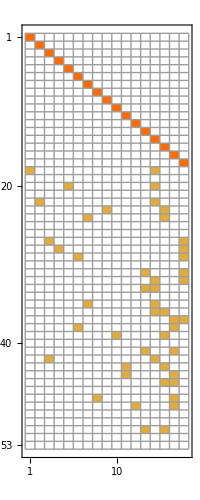

```mathematica
MatrixPlot[Transpose@#,MaxPlotPoints->∞,Mesh->All]&/@R//GraphicsRow//Show[#,ImageSize->Large]&
```